```mathematica
Quit[];
```

```mathematica
<<Matchete`
```

v0.1.5

by Javier Fuentes-Martín, Matthias König, Julie Pagès, Anders Eller Thomsen, and Felix Wilsch 
Reference: [arXiv:2212.04510](https://arxiv.org/abs/2212.04510)
Website: https://gitlab.com/matchete/matchete

## Definition of the model

### Gauge group, fields and coupling

Define gauge group

```mathematica
DefineGaugeGroup[SU3c,SU[3],gs,G,FundAlphabet->{"a","b","c","d","e","f"},AdjAlphabet->{"A","B","C","D","E","F"}]
```

Define fields

```mathematica
DefineField[t,Fermion,Indices->{SU3c[fund]},Mass->{Light,MT}]
DefineField[sT,Scalar, Indices->{SU3c[fund]},Mass->{Heavy,mST}]
DefineField[chi, Fermion, Mass->{Heavy,mChi}]
```

Define coupling

```mathematica
DefineCoupling[yDM,SelfConjugate->True]
```

### Lagrangian

Write interactions

```mathematica
Lint=-yDM[] Bar@t[a]**PR**chi[] sT[a]//PlusHc;
```

Define Lagrangian

```mathematica
LUV=FreeLag[]+Lint;
LUV//NiceForm
CheckLagrangian[LUV]
```

-1/4(G^μνA)^2+D_μOverBar[sT]_aD_μsT^a-mST^2 OverBar[sT]_a sT^a+ⅈ(OverBar[chi]·γ_μ·D_μchi)-mChi(OverBar[chi]·chi)+ⅈ((t̄)_a·γ_μ·D_μt^a)-MT((t̄)_a·t^a)-yDM OverBar[sT]_a(OverBar[chi]·P_L·t^a)-yDM sT^a((t̄)_a·P_R·chi)

True

Lagrangian of only light degrees of freedom

```mathematica
Llight= FreeLag[t,G];
%//NiceForm
```

-1/4(G^μνA)^2+ⅈ((t̄)_a·γ_μ·D_μt^a)-MT((t̄)_a·t^a)

## Matching to the effective Lagrangian

### One-loop

#### Matching

```mathematica
LEFT=Match[LUV,LoopOrder->1,EFTOrder->6];
```

#### Removing redundant operators off-shell

Simplify to the Green basis using integration by parts and collect Hermitian conjugate terms in + H.c.

```mathematica
LEFTOffShell=LEFT //GreensSimplify;
LEFTOffShell//HcSimplify //NiceForm
```

(-1/4+ℏ (-1/24 1/ϵ gs^2-1/24 gs^2 Log[(μ̄)^2/mST^2]))(G^μνA)^2+ⅈ((t̄)_a·γ_μ·D_μt^a)-MT((t̄)_a·t^a)+ℏ (ⅈ/2 1/ϵ yDM^2+ⅈ/4 yDM^2 (1+2LF_(2,1,-1)[mST,mChi]))((t̄)_a·γ_μ P_L·D_μt^a)-1/120 ℏ gs^2 1/mST^2 D_νG^μνAD_ρG^μρA+(ⅈ/2 ℏ yDM^2 (LF_(3,1,-1)[mST,mChi]-LF_(4,1,-2)[mST,mChi])(D^2(t̄)_a·γ_ν P_L·D_νt^a)+H.c.)+1/360 ℏ gs^3 1/mST^2 G^μνB G^μρC G^νρA f^ABC-1/6 ℏgs yDM^2 D_νG^μνA((t̄)_a·γ_μ P_L·t^b)T_b^Aa LF_(4,1,-2)[mST,mChi]+1/8 ℏ yDM^4((t̄)_a·γ_μ P_L·t^b)((t̄)_b·γ_μ P_L·t^a)LF_(2,2,-1)[mChi,mST]

```mathematica
LEFTsimp=(Normal[Series[LEFTOffShell,{yDM[],0,2}]]-Llight)/.{hbar->1/(16 Pi^2)}//CollectOperators ;
%//NiceForm
```

(-1/384 1/π^2 1/ϵ gs^2-1/384 1/π^2 gs^2 Log[(μ̄)^2/mST^2])(G^μνA)^2+ (ⅈ/32 1/π^2 1/ϵ yDM^2+ⅈ/64 1/π^2 yDM^2 (1+2LF_(2,1,-1)[mST,mChi]))((t̄)_a·γ_μ P_L·D_μt^a)-1/1920 1/π^2 gs^2 1/mST^2 D_νG^μνAD_ρG^μρA-ⅈ/32 1/π^2 yDM^2 (LF_(3,1,-1)[mST,mChi]-LF_(4,1,-2)[mST,mChi])(D_μ(t̄)_a·γ_μ P_L·D^2t^a)+ⅈ/32 1/π^2 yDM^2 (LF_(3,1,-1)[mST,mChi]-LF_(4,1,-2)[mST,mChi])(D^2(t̄)_a·γ_ν P_L·D_νt^a)+1/5760 1/π^2 gs^3 1/mST^2 G^μνB G^μρC G^νρA f^ABC-1/96 1/π^2 gs yDM^2 D_νG^μνA((t̄)_a·γ_μ P_L·t^b)T_b^Aa LF_(4,1,-2)[mST,mChi]

```mathematica
FullSimplify[EvaluateLoopFunctions[LEFTsimp]]//NiceForm
```

1/5760 1/π^2 (-15 1/ϵ gs^2 (1+ϵLog[(μ̄)^2/mST^2])(G^μνA)^2+90 ⅈ 1/ϵ yDM^2 (mChi^4 (2+3ϵ+2ϵLog[(μ̄)^2/mChi^2])-4 mChi^2 mST^2 (1+ϵ+ϵLog[(μ̄)^2/mST^2])+mST^4 (2+ϵ+2ϵLog[(μ̄)^2/mST^2]))((t̄)_a·γ_μ P_L·D_μt^a)1/((mChi^2-mST^2)^2)-3 gs^2 1/mST^2 D_νG^μνAD_ρG^μρA+30 ⅈ yDM^2 (2 mChi^6-6 mChi^2 mST^4+mST^6+3 mChi^4 mST^2 (1+2Log[(μ̄)^2/mChi^2]-2Log[(μ̄)^2/mST^2]))(D_μ(t̄)_a·γ_μ P_L·D^2t^a)1/((mChi^2-mST^2)^4)-30 ⅈ yDM^2 (2 mChi^6-6 mChi^2 mST^4+mST^6+3 mChi^4 mST^2 (1+2Log[(μ̄)^2/mChi^2]-2Log[(μ̄)^2/mST^2]))(D^2(t̄)_a·γ_ν P_L·D_νt^a)1/((mChi^2-mST^2)^4)+gs^3 1/mST^2 G^μνB G^μρC G^νρA f^ABC+10gs yDM^2 (18 mChi^4 mST^2-9 mChi^2 mST^4+2 mST^6+mChi^6 (-11-6Log[(μ̄)^2/mChi^2]+6Log[(μ̄)^2/mST^2]))D_νG^μνA((t̄)_a·γ_μ P_L·t^b)T_b^Aa 1/((mChi^2-mST^2)^4))

```mathematica
Expand[FullSimplify[Limit[1/5760 1/π^2 90 ⅈ 1/ϵ yDM^2 1/((mChi^2-mST^2)^2)(mChi^4 (2+3ϵ+2ϵLog[OverBar["μ"]^2/mChi^2])-4 mChi^2 mST^2 (1+ϵ+ϵLog[OverBar["μ"]^2/mST^2])+mST^4 (2+ϵ+2ϵLog[OverBar["μ"]^2/mST^2])),mChi->mST]]]
```

(ⅈ yDM^2 log((μ̄)^2/mST^2))/(32 π^2)+(ⅈ yDM^2)/(32 π^2 ϵ)

```mathematica
FullSimplify[1/5760 1/π^2(30 ⅈ yDM^2)Limit[1/((mChi^2-mST^2)^4)(2 mChi^6-6 mChi^2 mST^4+mST^6+3 mChi^4 mST^2 (1+2Log[OverBar["μ"]^2/mChi^2]-2Log[OverBar["μ"]^2/mST^2])),mChi->mST]]
```

(ⅈ yDM^2)/(384 π^2 mST^2)

```mathematica
FullSimplify[1/5760 1/π^2 10 gs yDM^2 Limit[1/((mChi^2-mST^2)^4)(18 mChi^4 mST^2-9 mChi^2 mST^4+2 mST^6+mChi^6 (-11-6Log[OverBar["μ"]^2/mChi^2]+6Log[OverBar["μ"]^2/mST^2])),mChi->mST]]
```

(gs yDM^2)/(384 π^2 mST^2)

#### Removing redundant operators on-shell

Simplify to the physical basis using field redefinitions. Scalar and fermion kinetic terms are canonically normalized.

```mathematica
LEFTOnShell=LEFT //EOMSimplify;
LEFTOnShellSimp=(LEFTOnShell//Matchete`PackageScope`ProjExpand//CollectOperators);
%//NiceForm
```

(-1/4+ℏ (-1/24 1/ϵ gs^2-1/24 gs^2 Log[(μ̄)^2/mST^2]))(G^μνA)^2+ⅈ((t̄)_a·γ_μ·D_μt^a)+ (-MT+ℏ (1/4 1/ϵ MT yDM^2+1/8 MT yDM^2 (1+2LF_(2,1,-1)[mST,mChi]-4 MT^2 (LF_(3,1,-1)[mST,mChi]-LF_(4,1,-2)[mST,mChi]))))((t̄)_a·t^a)+1/360 ℏ gs^3 1/mST^2 G^μνB G^μρC G^νρA f^ABC+ⅈ/4 ℏgsMT yDM^2 (LF_(3,1,-1)[mST,mChi]-LF_(4,1,-2)[mST,mChi])G^μνA((t̄)_a·Γ_μν·t^b)T_b^Aa+1/480 ℏ (-2 gs^4 1/mST^2+15 yDM^4 LF_(2,2,-1)[mChi,mST]-20 gs^2 yDM^2 LF_(4,1,-2)[mST,mChi])((t̄)_a·γ_μ·t^b)((t̄)_b·γ_μ·t^a)+1/720 ℏ gs^2 (gs^2 1/mST^2+10 yDM^2 LF_(4,1,-2)[mST,mChi])((t̄)_a·γ_μ·t^a)((t̄)_b·γ_μ·t^b)+1/48 ℏ (-3 yDM^4 LF_(2,2,-1)[mChi,mST]+2 gs^2 yDM^2 LF_(4,1,-2)[mST,mChi])((t̄)_a·γ_μ·t^b)((t̄)_b·γ_μ γ_5·t^a)+1/32 ℏ yDM^4((t̄)_a·γ_μ γ_5·t^b)((t̄)_b·γ_μ γ_5·t^a)LF_(2,2,-1)[mChi,mST]-1/72 ℏ gs^2 yDM^2((t̄)_a·γ_μ·t^a)((t̄)_b·γ_μ γ_5·t^b)LF_(4,1,-2)[mST,mChi]

```mathematica
cGTT=SelectOperatorClass[LEFTOnShellSimp/.{hbar->1/(16 Pi^2)},{Bar@t,t},2]//Matchete`PackageScope`ProjExpand//CollectOperators;
%//NiceForm
```

ⅈ/64 1/π^2 gsMT yDM^2 (LF_(3,1,-1)[mST,mChi]-LF_(4,1,-2)[mST,mChi])G^μνA((t̄)_a·Γ_μν·t^b)T_b^Aa

```mathematica
cGTTexp=FullSimplify[cGTT//EvaluateLoopFunctions,Assumptions->{mST>0,mChi>0,μbar2>0}];
%//NiceForm
```

-ⅈ/384 1/π^2 gsMT yDM^2 (2 mChi^6-6 mChi^2 mST^4+mST^6+3 mChi^4 mST^2 (1+2Log[1/mChi^2]-2Log[1/mST^2]))G^μνA((t̄)_a·Γ_μν·t^b)T_b^Aa 1/((mChi^2-mST^2)^4)

```mathematica
A0 = Simplify[-I cGTTexp/.{FieldStrength[a_,b_,c_,d_]->1,Bar[a_]->1,Field[a_,b_,c_,d_]->1,DiracProduct[a_]->1,CG[a_,b_]->1,Coupling[a_,b_,c_]->a}]
```

-(gs MT yDM^2 (-6 mChi^2 mST^4+3 mChi^4 mST^2 (2 log(1/mChi^2)-2 log(1/mST^2)+1)+2 mChi^6+mST^6))/(384 π^2 (mChi^2-mST^2)^4)

```mathematica
ScientificForm[A0/.{mST->400.,mChi->300.,yDM->10.,gs->√1.6336281,MT->172.}]
```

-2.22341×10^-5

```mathematica
ScientificForm[A0/.{mST->5000.,mChi->4500.,yDM->10.,gs->√1.6336281,MT->172.}]
```

-1.2577×10^-7

```mathematica
ScientificForm[A0/.{mST->5000.,mChi->4999.9,yDM->10.,gs->√1.6336281,MT->172.}]
```

0.

```mathematica
A0limit=Normal[Series[A0,{mChi,mST,1}]]
```

(gs MT yDM^2 (mChi-mST))/(960 π^2 mST^3)-(gs MT yDM^2)/(768 π^2 mST^2)

```mathematica
A0limit0=Normal[Series[A0,{mChi,mST,0}]]
```

-(gs MT yDM^2)/(768 π^2 mST^2)

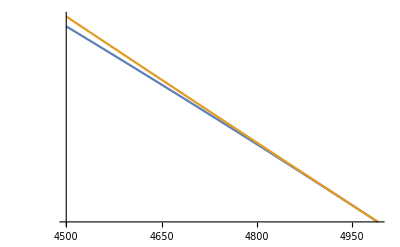

```mathematica
LogPlot[{A0limit/A0limit0/.{mST->5000.,yDM->10.,gs->√1.6336281,MT->172.},A0/A0limit0/.{mST->5000.,yDM->10.,gs->√1.6336281,MT->172.}},{mChi,4500,4990},PlotRange->All]
```

```mathematica
A0limit/.{mST->5000.,yDM->10.,gs->√1.6336281,MT->172.,mChi-> 4900.}
```

-1.17869×10^-7

```mathematica
A0limit/.{mST->5000.,yDM->10.,gs->√1.6336281,MT->172.,mChi-> 4900.}
```

-1.17869×10^-7